# Risk-free rate of return builder

Data source: http://mba.tuck.dartmouth.edu/pages/faculty/ken.french/data_library.html

```mathematica
ProcessDate[rawDate_]:=Block[{digits,year,month,day},
digits = IntegerDigits[rawDate];
year = FromDigits[Take[digits,{1,4}]];
month = FromDigits[Take[digits,{5,6}]];
day = FromDigits[Take[digits,{7,8}]];
DateObject[{year,month,day}]
];
```

## US Market

```mathematica
usMarketsData = Import[FileNameJoin[{NotebookDirectory[],"RawData","F-F_Research_Data_Factors_daily.CSV"}]];
```

```mathematica
rawData= Take[usMarketsData,{6,24542}];
```

```mathematica
dateRfRaw = rawData[[All,{1,5}]];
```

```mathematica
usRf = MapAt[ProcessDate,dateRfRaw,{All,1}];
```

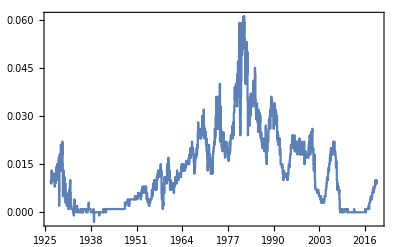

```mathematica
DateListPlot[usRf]
```

## Developed markets

```mathematica
developedMarketsData = Import[FileNameJoin[{NotebookDirectory[],"RawData","Developed_3_Factors_Daily.csv"}]];
```

```mathematica
rawData= Take[developedMarketsData,{8,7595}];
```

```mathematica
dateRfRaw = rawData[[All,{1,5}]];
```

```mathematica
devRf = MapAt[ProcessDate,dateRfRaw,{All,1}];
```

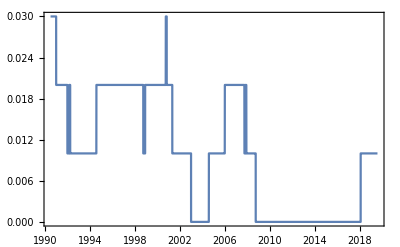

```mathematica
DateListPlot[devRf]
```

## Emerging markets

```mathematica
ProcessShortDate[rawDate_]:=Block[{digits,year,month},
digits = IntegerDigits[rawDate];
year = FromDigits[Take[digits,{1,4}]];
month = FromDigits[Take[digits,{5,6}]];
DateObject[{year,month}]
];
DaysInMonth[date_]:=QuantityMagnitude[DateDifference[date,DatePlus[date,{1,"Month"}]]];
```

```mathematica
emergingMarketsData = Import[FileNameJoin[{NotebookDirectory[],"RawData","Emerging_5_Factors.csv"}]];
```

```mathematica
rawData= Take[emergingMarketsData,{8,369}];
```

```mathematica
dateRfRaw = rawData[[All,{1,7}]];
```

```mathematica
montlyEmergingRf = MapAt[ProcessShortDate,dateRfRaw,{All,1}];
```

```mathematica
emergingRf = Map[{First[#],Last[#]/DaysInMonth[First[#]]}&,montlyEmergingRf];
```

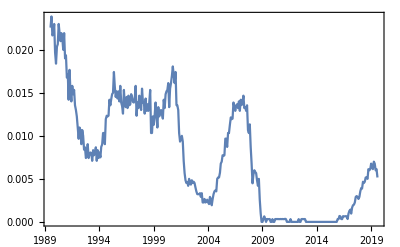

```mathematica
DateListPlot[emergingRf]
```

## Results

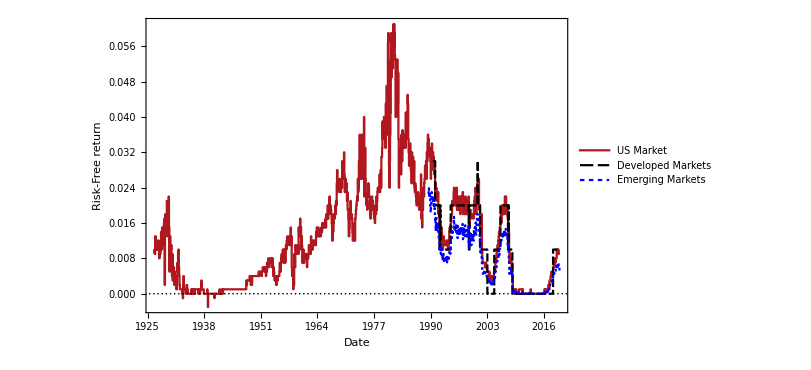

```mathematica
DateListPlot[
{usRf,devRf,emergingRf},
PlotRange->All,
ImageSize->600,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",15],Style["Risk-Free return",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotStyle->{ColorData["Legacy"]["IndianRed"],Black,Blue},
PlotLegends->Placed[LineLegend[{"US Market","Developed Markets","Emerging Markets"},LegendFunction->(Framed[#,Background->Opacity[0.6,White]]&),LabelStyle->11],{Left,Top}],
GridLines->{{},{0}}
]
```

## Database builder

```mathematica
usDatabase = <|"Name"->"US Market","DateReturns"->usRf|>;developedDatabase = <|"Name"->"Developed Markets","DateReturns"->devRf|>;
emergingDatabase = <|"Name"->"Emerging Markets","DateReturns"->emergingRf|>;
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"RiskFreeRet_Database.wdx"}],{usDatabase,developedDatabase,emergingDatabase}]
```

/home/carlos/Documentos/Programacion/EconomicComputations/Datasets/RiskFreeReturn/RiskFreeRet_Database.wdx